```mathematica
Dc=0.76;
Fc=0.5;
fc=0.093;
```

```mathematica
dgpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-dleta-pi-xi1.wdx"];
dHdgu=Query[1,1]@dgpdu;
dHeru=Query[1,2]@dgpdu;

dEdgu=Query[2,1]@dgpdu;
dEeru=Query[2,2]@dgpdu;


dHerf=Interpolation[Flatten[dHeru,1]];dEerf=Interpolation[Flatten[dEeru,1]];
```

```mathematica
dEerf[0.05,-1]
```

0.

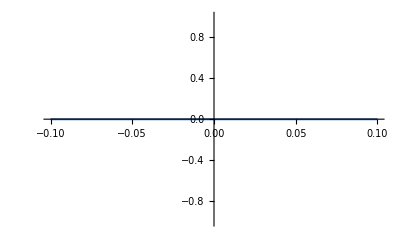

```mathematica
Plot[dEerf[x,-1],{x,-0.1,0.1}]
```

```mathematica
gpdu=Import["G:\\calc-online\\gpd\\3dre\\gpd3d-d-up-xi1-pi-noD.wdx"];
Hdgu=Query[1,1]@gpdu;
Heru=Query[1,2]@gpdu;
Hdau=Query[1,3]@gpdu;
Edgu=Query[2,1]@gpdu;
Eeru=Query[2,2]@gpdu;
Edau=Query[2,3]@gpdu;
Hdgf=Interpolation[Flatten[Hdgu,1]];
Herf=Interpolation[Flatten[Heru,1]];
```

```mathematica
Hdgf1[x_,t_]:=Chop[Hdgf[x,t],10^-7];
Herf1[x_,t_]:=Chop[Herf[x,t],10^-7];
```

```mathematica
(*别的都是0*)
```

```mathematica
Hdgfnu[x_,t_]:=Hdgf1[x,t];
Herfnu[x_,t_]:=Herf1[x,t]+dHerf[x,t];
```

```mathematica
(*d图和a图此时应该一样*)
```

```mathematica
(*d图当然也会对d给出贡献，但是*)
```

```mathematica
(*pi+，u就是输入，d的话输入是dbar，所以要改一下*)
```

```mathematica
piCoe1=(1/(2*(2π)^4))*(-I);
```

```mathematica
pi1Hdgu[x_,t_]:=piCoe1*Hdgfnu[x,t];
pi1Heru[x_,t_]:=piCoe1*Herfnu[x,t];
pi1Edgu[x_,t_]:=0;
pi1Eeru[x_,t_]:=0;
```

```mathematica
pi1Hdgd[x_,t_]:=-piCoe1*Hdgfnu[-x,t];
pi1Herd[x_,t_]:=-piCoe1*Herfnu[-x,t];
pi1Edgd[x_,t_]:=0;
pi1Eerd[x_,t_]:=0;
```

```mathematica
(*pi0，ud都是输入，也都存在，两者完全一样*)
```

```mathematica
piCoe0=(1/(2*(2π)^4))*(-I);
```

```mathematica
pi0Hdguz[x_,t_]:=piCoe0*(1/2)*Hdgfnu[x,t];
pi0Heruz[x_,t_]:=piCoe0*(1/2)*Herfnu[x,t];
pi0Edguz[x_,t_]:=0;
pi0Eeruz[x_,t_]:=0;
```

```mathematica
pi0Hdguf[x_,t_]:=-piCoe0*(1/2)*Hdgfnu[-x,t];
pi0Heruf[x_,t_]:=-piCoe0*(1/2)*Herfnu[-x,t];
pi0Edguf[x_,t_]:=0;
pi0Eeruf[x_,t_]:=0;

pi0Heruall[x_,t_]:=pi0Heruf[x,t]+pi0Heruz[x,t];
```

```mathematica
pi0Hdgdz[x_,t_]:=piCoe0*(1/2)*Hdgfnu[x,t];
pi0Herdz[x_,t_]:=piCoe0*(1/2)*Herfnu[x,t];
pi0Edgdz[x_,t_]:=0;
pi0Eerdz[x_,t_]:=0;
```

```mathematica
pi0Hdgdf[x_,t_]:=-piCoe0*(1/2)*Hdgfnu[-x,t];
pi0Herdf[x_,t_]:=-piCoe0*(1/2)*Herfnu[-x,t];
pi0Edgdf[x_,t_]:=0;
pi0Eerdf[x_,t_]:=0;

pi0Herdall[x_,t_]:=pi0Herdf[x,t]+pi0Herdz[x,t];
```